```mathematica
ClearGlobal[]:=(ClearAll["Global`*"];Clear[Derivative];);
```

```mathematica
ClearGlobal[]
```

```mathematica
RemoveGlobal[]:=(ClearGlobal[];Remove["Global`*"];);
```

```mathematica
RemoveGlobal[]
```

# Male Strategy and Rock-Paper-Scissors

## Game 1

### Payoff Matrix

Three types of males: Orange (aggressive polygamous), Yellow (“sneaky copulator”), and Blue (aggressive mate guarding monogamous).

```mathematica
table = {{"", "O", "Y", "B"}, {"O", "(0,0)", "(-1,1)","(1,-1)"}, {"Y", "(1,-1)", "(0,0)","(-1,1)"}, {"B", "(-1,1)", "(1,-1)","(0,0)"}}
```

{{,O,Y,B},{O,(0,0),(-1,1),(1,-1)},{Y,(1,-1),(0,0),(-1,1)},{B,(-1,1),(1,-1),(0,0)}}

```mathematica
Grid[table,ItemStyle->{FontFamily->"Latin Modern Roman"},Spacings->{2,.75}, Dividers->{{2->True},{2->True}}]
```

| O | Y | B
O | (0,0) | (-1,1) | (1,-1)
Y | (1,-1) | (0,0) | (-1,1)
B | (-1,1) | (1,-1) | (0,0)

### Replicator Dynamics

```mathematica
Subscript[p', 1] = (1-Subscript[p, 1]-2 Subscript[p, 2])Subscript[p, 1]
```

p_1 (1-p_1-2 p_2)

```mathematica
Subscript[p', 2] = (-1+2 Subscript[p, 1]+Subscript[p, 2])Subscript[p, 2]
```

p_2 (-1+2 p_1+p_2)

## Visualization

### Built-in Rendering with StreamPlot[] & DensityPlot[]

```mathematica
fig1dp := DensityPlot[(-1+2 Subscript[p, 1]+Subscript[p, 2])Subscript[p, 2], {Subscript[p, 1],0, 1}, {Subscript[p, 2],0, 1},RegionFunction->Function[{x,y},x + y<1], FrameLabel->{Defer[Subscript[p, 1]], Defer[Subscript[p, 2]]}, PlotRangePadding->None,LabelStyle->Black,BaseStyle->{FontSize->12},ColorFunction->(ColorData["ThermometerColors"][1.25*#1+.5]&),ColorFunctionScaling->False]
```

```mathematica
fig1s := StreamPlot[{(1-Subscript[p, 1]-2 Subscript[p, 2])Subscript[p, 1],(-1+2 Subscript[p, 1]+Subscript[p, 2])Subscript[p, 2]}, {Subscript[p, 1],0, 1}, {Subscript[p, 2],0, 1},RegionFunction->Function[{x,y},x + y<1], FrameLabel->{Defer[Subscript[p, 1]], Defer[Subscript[p, 2]]}, PlotRangePadding->None,LabelStyle->Black,BaseStyle->{FontSize->12}, StreamStyle->Black]
```

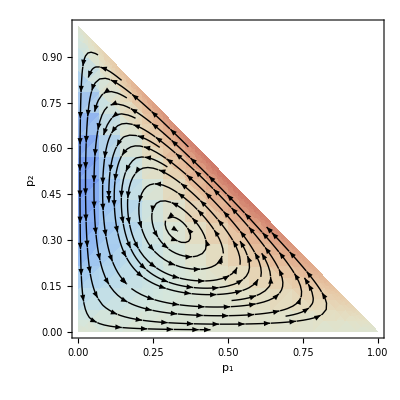

```mathematica
Show[fig1dp, fig1s]
```

### Custom streamDensityPlot (Supporting Code)

```mathematica
streamDensityPlot[f_,rx_,ry_,opts:OptionsPattern[]]:=(* Created by Jens U.Nöckel for Mathematica 8, updated by @Locus_of_ctrl for StreamPlot 01/2019 *)Module[{img,cont,pL,p,plotRangeRule,densityOptions,streamOptions,frameOptions,rangeCoords},densityOptions=Join[FilterRules[{opts},FilterRules[Options[DensityPlot],Except[{ImageSize,Prolog,Epilog,FrameTicks,PlotLabel,ImagePadding,GridLines,Mesh,AspectRatio,PlotRangePadding,Frame,Axes}]]],{PlotRangePadding->None,ImagePadding->None,Frame->None,Axes->None}];
pL=DensityPlot[f,rx,ry,Evaluate@Apply[Sequence,densityOptions]];
p=First@Cases[{pL},Graphics[__],∞];
plotRangeRule=FilterRules[Quiet@AbsoluteOptions[p],PlotRange];
streamOptions=Join[FilterRules[{opts},FilterRules[Options[StreamPlot],Except[{Prolog,Epilog,FrameTicks,Background,Frame,Axes}]]],{Frame->None,Axes->None}];
(* The density plot img and stream plot cont are created here:*)img=Rasterize[p,"Image", Background->None];
cont=If[MemberQ[{0,None},(streams/.FilterRules[{opts},streams])],{},StreamPlot[f,rx,ry,Evaluate@Apply[Sequence,streamOptions]]];
(* Before showing the plots,set the PlotRange for the frame which will be drawn separately: *)frameOptions=Join[FilterRules[{opts},FilterRules[Options[Graphics],Except[{PlotRangeClipping,PlotRange}]]],{plotRangeRule,Frame->True,PlotRangeClipping->True}];
rangeCoords=Transpose[PlotRange/.plotRangeRule];
(* To align the image img with the stream plot,enclose img in a bounding box rectangle of the same dimensions as cont,
and then combine with cont using Show: *)
(* @Locus_of_crrl: Instead of setting alpha channel inside Show[],
I use Background->None in Rasterize[], which adds alpha channel automatically *) 
If[Head[pL]===Legended,Legended[#,pL[[2]]],#]&@Show[Graphics[{Inset[Show[img,AspectRatio->Full],rangeCoords[[1]],{0,0},rangeCoords[[2]]-rangeCoords[[1]]]},PlotRangePadding->None],cont,Evaluate@Apply[Sequence,frameOptions]]]
```

### Custom streamDensityPlot

This should give 7-10x more compact vector image output on export compared to built-in

```mathematica
streamDensityPlot[{(1-Subscript[p, 1]-2 Subscript[p, 2])Subscript[p, 1],(-1+2 Subscript[p, 1]+Subscript[p, 2])Subscript[p, 2]}, {Subscript[p, 1],0, 1}, {Subscript[p, 2],0, 1},RegionFunction->Function[{x,y},x + y<1], ColorFunction->(ColorData["ThermometerColors"][#1+.5]&),ColorFunctionScaling->False,FrameLabel->{Defer[Subscript[p, 1]], Defer[Subscript[p, 2]]}, PlotRangePadding->None,LabelStyle->Black,BaseStyle->{FontSize->12}, StreamStyle->Black]
```

-Graphics-

### Ternary Diagram (Supporting Code)

```mathematica
{error,xf}=FindGeometricTransform[{{0,0},{1,0},{1,Tan[Pi/3]}/2},{{0,0},{1,0},{0,1}}];
```

```mathematica
ClearAll[tickGraphics,triangleTicks];
Module[{ticklen=0.025,(*length of ticks (const parameter)*)textoffset=0.04},tickGraphics[tickrange:{0.,total_},angle_]:=With[{rotSideXF=RotationTransform[angle,total {1.,Tan[Pi/6]}/2.]},{Line[rotSideXF/@Thread[{tickrange,0}]],With[{rotTickXF=Composition[RotationTransform[π/3.,rotSideXF@{#,0.}],rotSideXF]},{Text[NumberForm[N@#,{3,2}],rotTickXF[total {-ticklen-textoffset,0}+{#,0.}],{0,0.}],{Line[rotTickXF/@{total {-ticklen,0}+{#,0.},{#,0.}}]}}]&/@Select[N@FindDivisions[tickrange,4],0.≤#≤total&]}];
triangleTicks[g_Graphics,total_: 1]:=Show[Graphics[First@g],Graphics[{AbsoluteThickness[0.5],Table[tickGraphics[{0.,total},N@angle],{angle,0,4 Pi/3,2 Pi/3}]}],Axes->False,Frame->None,PlotRange->total {{0,1+ticklen},{0,Sqrt[3]/2+ticklen/2}},PlotRangePadding->0.07 total,PlotRangeClipping->False,ImagePadding->{{20,5},{20,5}}]]
```

### Ternary Diagram

Repeating the above plot except without the frame:

```mathematica
dp = streamDensityPlot[{(1-Subscript[p, 1]-2 Subscript[p, 2])Subscript[p, 1],(-1+2 Subscript[p, 1]+Subscript[p, 2])Subscript[p, 2]}, {Subscript[p, 1],0, 1}, {Subscript[p, 2],0, 1},RegionFunction->Function[{x,y},x + y<1], ColorFunction->(ColorData["ThermometerColors"][#1+.5]&),ColorFunctionScaling->False,Frame->None, PlotRangePadding->None,LabelStyle->Black,BaseStyle->{FontSize->12}, StreamStyle->Black];
```

```mathematica
triangleTicks[Graphics[GeometricTransformation[First@dp,xf]]]
```

-Graphics-